```mathematica
DEList={{12845,12863,12915,12950,12965,12972,13150,13154,13216,13604,13734,13752,13800,13806,14134,14630,14673,14686,14695,14791,14820,14841,14853,14882,14893,14936,14960,14994,15144,15251,15433,15491,15621,15704,15774,15803,15876,15935,15956,16044,16053,16066,16072,16075,16081,16081,16125,16131,16133,16154,16201,16222,16301,16315,16336,16342,16356,16413,16424,16430,16444,16446,16461,16463,16470,16561,16601,16660,16663,16664,16672,16710,16714,16720,16725,17023,17060,17071,17275,17311,17445,17673,17792,17810,17812,18022,18104},{199,1070,245,1073,329,103,1547,1775,2614,2543,2046,1637,2135,2543,914,2625,2228,1832,738,1771,835,1828,352,711,2669,2419,2299,1714,269,2092,141,1896,2720,1825,1436,2166,2528,2361,561,915,2724,2817,1134,737,1843,2745,2489,2696,2680,1810,2759,2371,1639,2458,1828,1901,1548,2680,1978,1898,2501,2488,2416,2479,1819,1244,1213,568,338,2221,569,286,1445,1820,190,729,1541,2634,1726,433,542,1445,2228,1541,241,2474,733}};
index=1

GPSDay=DEList[[1,index]]
Event=DEList[[2,index]]

BiasData=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/dataStream_",ToString[GPSDay],"_",ToString[Event],".txt"],"Table"];
Template=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/signalTemplate",ToString[GPSDay],"-",ToString[Event],".out"],"Table"];
Eij=Import[StringJoin["/Users/nv/Downloads/results/oc3Eij/oc3Eij",ToString[GPSDay],".out"],"Table"];
info=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/info",ToString[GPSDay],".out"],"Table"][[5,All]];
htemp=-0.0679241;

Einv=Inverse[Eij];
Flattemplate=Flatten[Template];
V=Einv.Flatten[BiasData]/Sqrt[Transpose[Flattemplate].Einv.Flattemplate];
SNR=Flattemplate.V
```

1

12845

199

-6.15573

```mathematica
Data=Partition[V,61];
sortedPairs=SortBy[Transpose[{Template, Data,info}],First[Position[Template,1]]];
sorted1=sortedPairs[[All,1]];
sorted2=sortedPairs[[All,2]];
sorted3=sortedPairs[[All,3]];
```

```mathematica
Length[BiasData]
DW=Reverse[sorted2];
```

20

```mathematica
Length[Template]
S=Sign[SNR]*Reverse[sorted1];
```

20

```mathematica
Finish=First[Position[sorted1,1]][[2]]
```

33

```mathematica
Start=Last[Position[sorted1,1]][[2]]
```

30

```mathematica
spacing=0.16;
```

```mathematica
TileCount=Total[Total[Abs[Template]]]
```

24

```mathematica
Max2=SNR/TileCount;
Min2=-1.0*Max2;
```

```mathematica
Max[DW]
```

1.10374

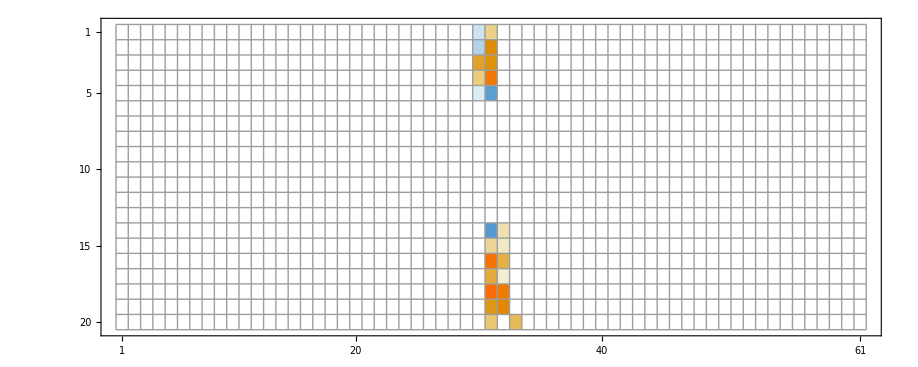

```mathematica
ContributionChart=MatrixPlot[Partition[Flatten[S]*Flatten[DW],61],Mesh->All]
```

```mathematica
SNRContribution=Partition[Flatten[S]*Flatten[DW],61];
SNRContribution//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0633448 | 0.24031 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.13213 | 0.483573 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.42034 | 0.479294 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.244748 | 0.676555 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0544594 | -0.554863 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.605344 | 0.123616 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.214989 | 0.0608688 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.741479 | 0.383666 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.388285 | 0.0412148 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.80642 | 0.669575 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.47421 | 0.525347 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.25107 | 0. | 0.340312 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Max2
```

-0.256489

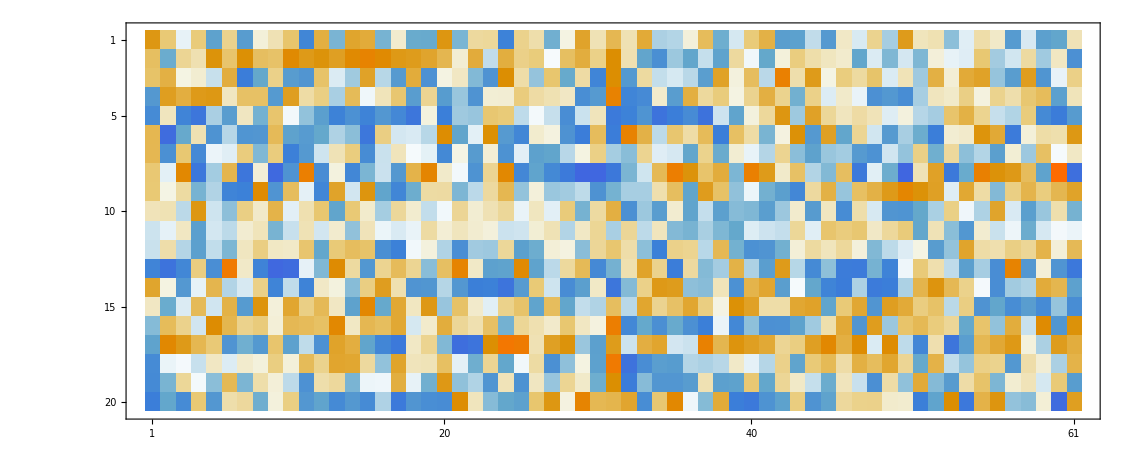

```mathematica
MatrixPlot[DW]
```

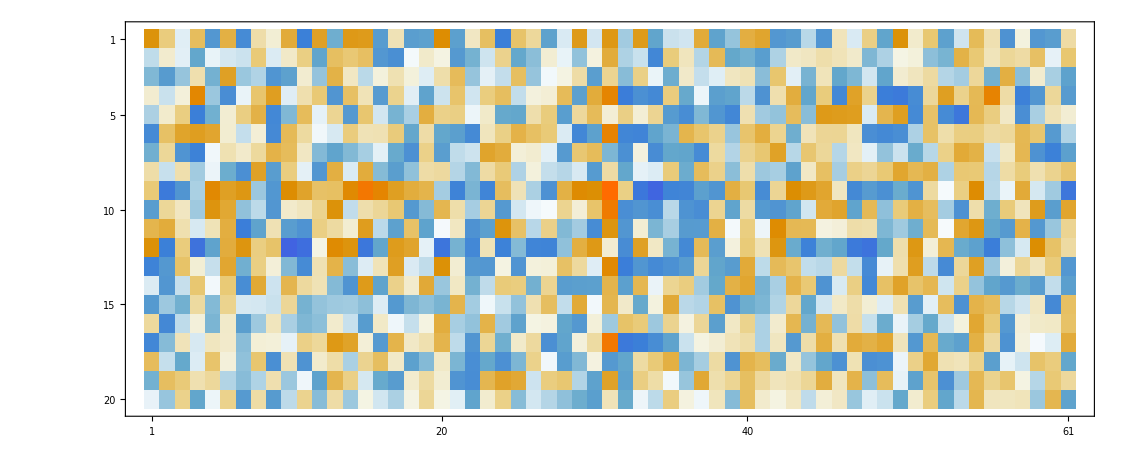

```mathematica
MatrixPlot[BiasData]
```

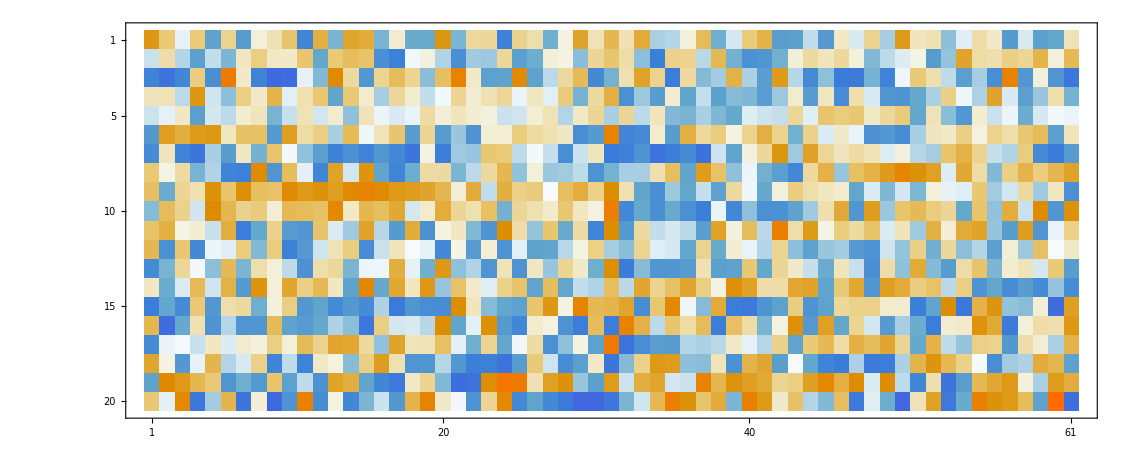

```mathematica
MatrixPlot[Data]
```

```mathematica
Total[Flatten[S]*Flatten[DW]]
```

6.15573

```mathematica
Max[DW]
Min[DW]
```

1.10374

-0.883284

```mathematica
Mean[Mean[Abs[DW]]]
```

0.199274

```mathematica
Max[Max[DW],Abs[Min[DW]]]
```

1.10374

```mathematica
newArray=Transpose[Transpose[DW][[Start;;Finish]]];
```

```mathematica
newArray//MatrixForm
```

(0.0633448 | 0.24031 | 0.0651509 | 0.310083
0.13213 | 0.483573 | 0.0706026 | -0.177833
-0.42034 | 0.479294 | -0.258657 | 0.0978656
-0.244748 | 0.676555 | -0.42015 | -0.360351
0.0544594 | -0.554863 | -0.45507 | -0.288553
0.219551 | -0.502328 | 0.670869 | 0.269946
0.137428 | -0.0790573 | -0.118049 | 0.121002
-0.864221 | -0.57266 | -0.135121 | -0.0375166
-0.296769 | -0.141575 | -0.0771745 | -0.0775477
0.0947686 | 0.281132 | -0.31666 | -0.0925177
0.113888 | -0.0744131 | 0.111542 | -0.0579584
0.111935 | 0.183435 | 0.0822184 | -0.114081
-0.367882 | -0.141663 | 0.0732326 | 0.344835
0.0400729 | -0.605344 | -0.123616 | 0.131247
-0.0678659 | 0.214989 | -0.0608688 | 0.334221
0.00717369 | 0.741479 | -0.383666 | -0.162743
-0.2106 | 0.388285 | -0.0412148 | 0.284187
-0.205074 | 0.80642 | -0.669575 | -0.33996
-0.151982 | 0.47421 | -0.525347 | -0.121903
0.238297 | 0.25107 | 0.334239 | -0.340312)

```mathematica
Max[Max[newArray],Abs[Min[newArray]]]
```

0.864221

```mathematica
Mean[Abs[Flatten[newArray]]]
```

0.262411

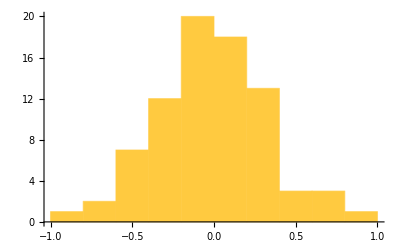

```mathematica
Histogram[Flatten[newArray]]
```

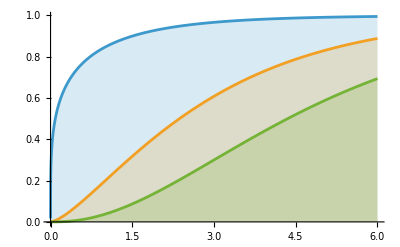

```mathematica
Plot[Table[CDF[ChiSquareDistribution[ν],x],{ν,{0.5,3,5}}]//Evaluate,{x,0,6},Filling->Axis]
```

```mathematica
dist=ChiSquareDistribution[79];
xValue=Quantile[dist,1-5.802891933*10^-7]
```

155.823

```mathematica
Dimensions[Einv]
```

{1220,1220}

```mathematica
NumClocks=Length[Template]
JW=61;
NewJW=Finish-Start+1
NewSize=NumClocks*NewJW
ETrimmed=ConstantArray[0,{NewSize,NewSize}];
```

20

4

80

```mathematica
For[a=0,a<NumClocks,a++,
For[s=1,s<=NewJW,s++,
For[b=0,b<NumClocks,b++,
For[S=1,S<=NewJW,S++,
ETrimmed[[NewJW*b+S,NewJW*a+s]]=Eij[[JW*b+S-1+Start,JW*a+s-1+Start]];
];
];
];
];
```

```mathematica
ETrimmedinv=Inverse[ETrimmed]
```

```mathematica
Dimensions[ETrimmedinv]
```

{80,80}

```mathematica
SNRContributionTrimmed=Transpose[Transpose[SNRContribution][[Start;;Finish]]];
SNRContributionTrimmed//MatrixForm
newArray//MatrixForm
```

(-0.0633448 | 0.24031 | 0. | 0.
-0.13213 | 0.483573 | 0. | 0.
0.42034 | 0.479294 | 0. | 0.
0.244748 | 0.676555 | 0. | 0.
-0.0544594 | -0.554863 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.605344 | 0.123616 | 0.
0. | 0.214989 | 0.0608688 | 0.
0. | 0.741479 | 0.383666 | 0.
0. | 0.388285 | 0.0412148 | 0.
0. | 0.80642 | 0.669575 | 0.
0. | 0.47421 | 0.525347 | 0.
0. | 0.25107 | 0. | 0.340312)

(0.0633448 | 0.24031 | 0.0651509 | 0.310083
0.13213 | 0.483573 | 0.0706026 | -0.177833
-0.42034 | 0.479294 | -0.258657 | 0.0978656
-0.244748 | 0.676555 | -0.42015 | -0.360351
0.0544594 | -0.554863 | -0.45507 | -0.288553
0.219551 | -0.502328 | 0.670869 | 0.269946
0.137428 | -0.0790573 | -0.118049 | 0.121002
-0.864221 | -0.57266 | -0.135121 | -0.0375166
-0.296769 | -0.141575 | -0.0771745 | -0.0775477
0.0947686 | 0.281132 | -0.31666 | -0.0925177
0.113888 | -0.0744131 | 0.111542 | -0.0579584
0.111935 | 0.183435 | 0.0822184 | -0.114081
-0.367882 | -0.141663 | 0.0732326 | 0.344835
0.0400729 | -0.605344 | -0.123616 | 0.131247
-0.0678659 | 0.214989 | -0.0608688 | 0.334221
0.00717369 | 0.741479 | -0.383666 | -0.162743
-0.2106 | 0.388285 | -0.0412148 | 0.284187
-0.205074 | 0.80642 | -0.669575 | -0.33996
-0.151982 | 0.47421 | -0.525347 | -0.121903
0.238297 | 0.25107 | 0.334239 | -0.340312)

```mathematica
DmS=Flatten[Transpose[Transpose[BiasData][[Start;;Finish]]]-htemp*Transpose[Transpose[Template][[Start;;Finish]]]];
```

```mathematica
Transpose[DmS].ETrimmedinv.DmS
```

142.02

```mathematica
Transpose[Flatten[BiasData-htemp*Template]].Einv.Flatten[BiasData-htemp*Template]
```

1290.8